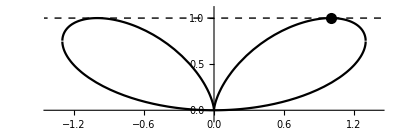

```mathematica
Plot[
Flatten@Values @ Solve[(x^2+y^2)^2==4x^2 y,y],
{x,-1.5,1.5},
PlotStyle->Black,
PlotRange->{{-1.4,1.4},{-.1,1.1}},
AspectRatio->1/3,
Epilog->{
PointSize@0.02,Point[{1,1}],
Dashed,InfiniteLine[{1,1},{1,0}]
}
]
```

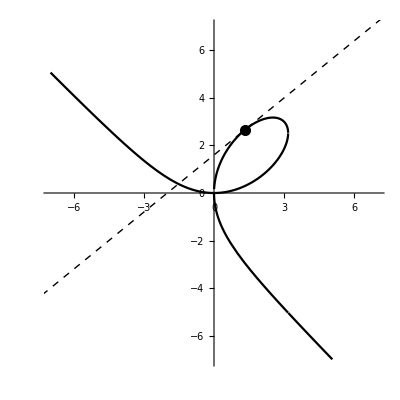

```mathematica
Plot[
Flatten@Values @ Solve[x^3+y^3-6x y==0,y],
{x,-7,7},
PlotStyle->Black,
PlotRange->{{-7,7},{-7,7}},
AspectRatio->1,
Epilog->{
PointSize@0.02,Point[{4/3,8/3}],
Dashed,InfiniteLine[{4/3,8/3},{5,4}]
}
]
```

```mathematica
Manipulate[
ParametricPlot[
{a Cos[t],b Sin[t]},
{t,-10,10},
PlotRange->{{-10,10},{-10,10}},
PlotStyle->Black,
Epilog->{
PointSize@0.02,Blue,Point[Flatten@{Flatten@Values@Solve[x^2/a^2+(-b^2x/a^2)^2/b^2==1,x][[1]],-b^2(Flatten@Values@Solve[x^2/a^2+(-b^2x/a^2)^2/b^2==1,x][[1]])/a^2}],
Point[Flatten@{Flatten@Values@Solve[x^2/a^2+(-b^2x/a^2)^2/b^2==1,x][[2]],-b^2(Flatten@Values@Solve[x^2/a^2+(-b^2x/a^2)^2/b^2==1,x][[2]])/a^2}],
Dashed,InfiniteLine[Flatten@{Flatten@Values@Solve[x^2/a^2+(-b^2x/a^2)^2/b^2==1,x][[1]],-b^2(Flatten@Values@Solve[x^2/a^2+(-b^2x/a^2)^2/b^2==1,x][[1]])/a^2},{1,1}],
InfiniteLine[Flatten@{Flatten@Values@Solve[x^2/a^2+(-b^2x/a^2)^2/b^2==1,x][[2]],-b^2(Flatten@Values@Solve[x^2/a^2+(-b^2x/a^2)^2/b^2==1,x][[2]])/a^2},{1,1}],
Red,Dashing[None],Point[{a Cos[t],b Sin[t]}],
InfiniteLine[{a Cos[t],b Sin[t]},{a^2(b Sin[t]),-b^2 a Cos[t]}]
}
],
{{a,8},1,8, Appearance->Labeled},
{{b,5},1,8, Appearance->Labeled},
{{t,Pi/4},0,2Pi, Appearance->Labeled}
]
```